$Aborted

ReplaceAll::reps: {bestFit} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

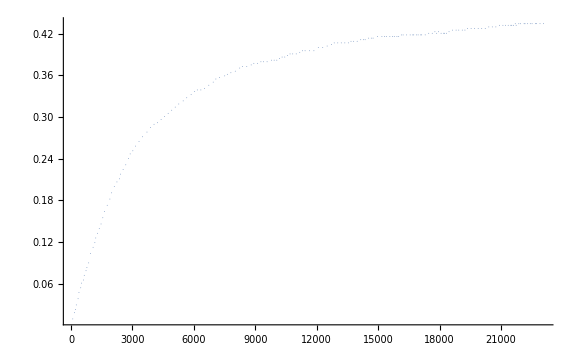

```mathematica
ClearAll["Global`*"];
(* The complete equations in terms of the polarizations Subscript[P, n], Subscript[P, e], and Subscript[Q, n] *)
pn0=0;
pe0=-1;
ϕ1=ϕ2=0;
ω1=1/t1e;
θ=(2c t1e)/t1n;
σ=0;
physicalTimes={t1e->0.03,t1n->1.5*60*60};
peDot=ω1(α(-4/3 pe[t]+pn[t]+1/3 pe[t]qn[t])+β(-4/3 pe[t]-pn[t]+1/3 pe[t]qn[t])-2s pe[t]+σ((2/3 qn[t]-8/3)(pe[t]-pe0)+2pn0 pe[t]pn[t])-2(pe[t]-pe0));
pnDot=ω1 c(α(2/3 pe[t]-1/2 pn[t]-1/6 pe[t]qn[t])+β(-2/3 pe[t]-1/2 pn[t]+1/6 pe[t]qn[t])+θ(-pn[t]-1/3 pn0 qn[t]+4/3 pn0)+σ(-pe0 pe[t]pn[t]-pn[t]-1/3 pn0 qn[t]+4/3 pn0))+ω1 ϕ1(4/3 pn0-1/3 pn0 qn[t]-pn[t])+ω1 ϕ2(4/3 pn0+2/3 pn0 qn[t]-2pn[t]);
qnDot=ω1 c(α(3/2 pe[t]pn[t]-3/2 qn[t])+β(-3/2 pe[t]pn[t]-3/2 qn[t])+θ(3pn0 pn[t]-3qn[t])+σ(3pe0 pe[t]qn[t]+3pn0 pn[t]-3qn[t]))+ϕ1 ω1(3pn0 pn[t]-3qn[t]);
eqns={pe'[t]==peDot,pn'[t]==pnDot,qn'[t]==qnDot,
pe[0]==-1,pn[0]==0,qn[0]==0};
sol=ParametricNDSolve[eqns/.physicalTimes,{pe,pn,qn},{t,0,25000},{c,α,β,s}];

someData=Table[{t,pn[1*^-4,0,5,0][t]/.sol},{t,0,2000}];
realData=Import["realdata.csv"];
bestFit=FindFit[realData,
{pn[c,α,β,s][t]/.sol,{0.5*^-4≤c≤10*^-4,0≤α≤7,0≤β≤7,0≤s≤7}},
{c,α,β,s},t]
Show[Plot[pn[c,α,β,s][t]/.bestFit/.sol,{t,0,23000},PlotStyle->{{Orange,Thick}}],ListPlot[realData,PlotStyle->PointSize[0.001]],
ImageSize->Large,
PlotRange->All]
```